# Occupied Volume: An atom specific %VBur calculator

Ben Shields
7/15/19

## Example 1: Labeled Gaussian 16 output files

Load the script.

```mathematica
<<(NotebookDirectory[]<>"\\occupied_volume.wls")
```

Extract optimized coordinates from a Gaussian .log file.

```mathematica
ExtractCoordinates[NotebookDirectory[]<>"\\example_data\\direct_arylation_imidazole_26123.log"];
coordinateList//TableForm
```

C | -1.129366 | 1.181040 | -0.238242
C | -2.521710 | 1.120002 | -0.228290
N | -3.225597 | 0.002602 | -0.008540
C | -2.521603 | -1.112560 | 0.221983
C | -1.129382 | -1.169323 | 0.253418
C | -0.411766 | 0.006808 | 0.011249
N1 | 1.000435 | 0.006099 | 0.016847
C2 | 1.829210 | -1.028986 | -0.367061
H | 1.435009 | -1.963715 | -0.740923
N3 | 3.096931 | -0.714050 | -0.271442
C4 | 3.112778 | 0.582822 | 0.203036
H | 4.043645 | 1.099241 | 0.394208
C5 | 1.840187 | 1.052989 | 0.379309
H6 | 1.453449 | 1.985029 | 0.760746
H | -0.619919 | 2.113230 | -0.457239
H | -3.101754 | 2.021382 | -0.417923
H | -3.101510 | -2.015264 | 0.405430
H | -0.621380 | -2.099204 | 0.485244

In this calculation the atoms were labeled numerically. Compute the % occupied volume for the atom labeled 1.

```mathematica
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\direct_arylation_imidazole_26123.log",1]
```

0.658431

Compute the % occupied volume for all labeled atoms.

```mathematica
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\direct_arylation_imidazole_26123.log",#]&/@Range[6]
```

{0.658431,0.51859,0.447829,0.456944,0.526265,0.390261}

Generate a graphical representation of the % occupied volume for atom 6.

```mathematica
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\direct_arylation_imidazole_26123.log",6]

atomStyle[atom_]:=Which[
	StringContainsQ[atom,"C"],
	Black,
	StringContainsQ[atom,"H"],
	White,
	StringContainsQ[atom,"N"],
	Blue,
	StringContainsQ[atom,"O"],
	Red,
	True,
	ColorData[68,2]
];

g1=Graphics3D[{atomStyle[atomLabels[[#]]],Specularity[White,10],Sphere[allCoordinatesPlot[[#]],radiiPlot[[#]]]}&/@Range[allCoordinatesPlot//Count[_]]];

Quiet@Show[
	g1,
	Graphics3D[
		{
			Opacity[0.6],
			ColorData[97,1],
			Glow[ColorData[97,1]],
			Sphere[atomPositionPlot,setRadius]
		}
	],
	Boxed->False,
	ViewPoint->Top
]
```

0.390261

-Graphics3D-

## Example 2: Unlabeled Gaussian 16 output files

Load the script.

```mathematica
<<(NotebookDirectory[]<>"\\occupied_volume.wls")
```

Extract optimized coordinates from a Gaussian .log file.

```mathematica
ExtractCoordinates[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log"];
coordinateList//TableForm
```

N | 2.196928 | -0.026555 | -0.000016
C | 2.717182 | 1.217653 | 0.000006
N | 1.739721 | 2.219130 | 0.000093
N | 0.437562 | 1.796389 | 0.000094
C | -0.303776 | 2.904955 | 0.000241
C | 0.518590 | 4.052481 | 0.000328
C | 1.812941 | 3.583967 | 0.000234
C | 4.082914 | 1.493352 | -0.000045
C | 4.960317 | 0.413138 | -0.000116
C | 4.443494 | -0.882925 | -0.000128
C | 3.064350 | -1.057878 | -0.000077
H | -1.379176 | 2.821412 | 0.000256
H | 0.200862 | 5.084234 | 0.000448
H | 2.760161 | 4.100672 | 0.000260
H | 4.446881 | 2.514140 | -0.000032
H | 6.032163 | 0.586154 | -0.000159
H | 5.093305 | -1.750951 | -0.000176
H | 2.603341 | -2.040312 | -0.000080
Ni | 0.189575 | -0.035756 | 0.000008
C | -1.664295 | 0.199141 | -0.000024
C | -2.380423 | 0.353079 | -1.196776
C | -2.380719 | 0.351867 | 1.196706
C | -3.747607 | 0.644369 | -1.197550
H | -1.875375 | 0.236620 | -2.154163
C | -3.747895 | 0.643178 | 1.197430
H | -1.875919 | 0.234386 | 2.154095
C | -4.458462 | 0.792903 | -0.000073
H | -4.271144 | 0.753969 | -2.146432
H | -4.271664 | 0.751833 | 2.146292
I | -0.116888 | -2.609479 | -0.000030
C | -5.945004 | 1.069626 | -0.000113
H | -6.527537 | 0.137947 | -0.000567
H | -6.249127 | 1.638246 | 0.886288
H | -6.248939 | 1.638993 | -0.886099

In this calculation the atoms were not labeled numerically. Compute the % occupied volume for the unique atom Ni.

```mathematica
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log","Ni"]
```

0.748621

If the atom is not uniquely identified you will get an error.

```mathematica
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log","N"]
```

Unique atom N not found.

For unlabeled data you can select the atom by its position in the Cartesian matrix via the selectMatrixPosition option.

```mathematica
ExtractCoordinates[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log"];

nitrogenPositions=Position[coordinateList[[All,1]],"N"]//Flatten;

selectMatrixPosition=True;
OccupiedVolume[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log",#]&/@nitrogenPositions
```

{0.69729,0.677141,0.715519}

Generate a graphical representation of the % occupied volume around Ni.

```mathematica
(*Reset to the default settings*)
OccupiedVolumePresets;

OccupiedVolume[NotebookDirectory[]<>"\\example_data\\Ni_Ar_I_ligand_27123.log.log","Ni"]

atomStyle[atom_]:=Which[
	StringContainsQ[atom,"Ni"],
	Purple,
	StringContainsQ[atom,"C"],
	Black,
	StringContainsQ[atom,"H"],
	White,
	StringContainsQ[atom,"N"],
	Blue,
	StringContainsQ[atom,"O"],
	Red,
	True,
	ColorData[68,2]
];

g2=Graphics3D[{atomStyle[atomLabels[[#]]],Specularity[White,10],Sphere[allCoordinatesPlot[[#]],radiiPlot[[#]]]}&/@Range[allCoordinatesPlot//Count[_]]];

Quiet@Show[
	g2,
	Graphics3D[
		{
			Opacity[0.6],
			ColorData[97,1],
			Glow[ColorData[97,1]],
			Sphere[atomPositionPlot,setRadius]
		}
	],
	Boxed->False,
	ViewPoint->Top
]
```

0.748621

-Graphics3D-

## Numerical Integration

The numerical integrator I wrote for this application is not optimal. This is somewhat mitigated by the fact that the code is parallelizable (for example via the ParallelTable function). The integrator comes out of the box with a sparse grid which leads to a fair amount of error but fast evaluation time. You can increase the numerical accuracy (and the computation time) via the meshCount option.

```mathematica
(*Generate a test case with a known volume*)
testData={
	Ball[{0,0,0},1.2],
	Ball[{0,2.5,0},1.2],
	Ball[{0,5,0},1.2],
	Ball[{2.5,2.5,0},1.2],
	Ball[{-2.5,2.5,0},1.2]
};

intSphere=Sphere[{0,2.5,0},4];

Show@{Show[#,Boxed->False,ViewPoint->Top]&@(Graphics3D[{Black,#}]&@testData),Show[Graphics3D[{Opacity[0.6],ColorData[97,1],Glow[ColorData[97,1]],intSphere}]]}

totalVolume=(4/3*Pi*#^3)&/@{1.2,1.2,1.2,1.2,1.2}//Total;
sphereVolume=4/3*Pi*4.0^3;

testData={
	{"H1",0,0,0},
	{"H2",0,2.5,0},
	{"H3",0,5,0},
	{"H4",2.5,2.5,0},
	{"H5",-2.5,2.5,0}
};
```

-Graphics3D-

```mathematica
(*Track evaluation time with increasing meshCount*)
<<(NotebookDirectory[]<>"\\occupied_volume.wls")
occupiedVolumeInput="array";
setRadius=4.0;

eval=ParallelTable[
	(
		meshCount=n;
		time=AbsoluteTiming[vol=OccupiedVolume[testData,2]][[1]];
		{n,vol,time}
	),
	{n,{5,10,15,20,25,30,35,40,45,50}}
];
```

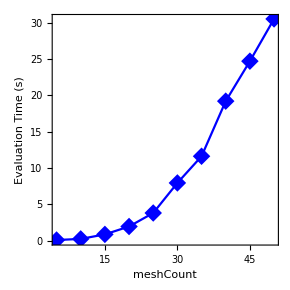
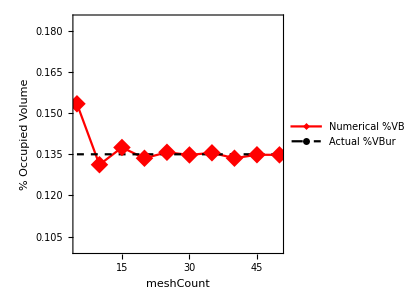

```mathematica
(*Plot the results*)
Row[{
	ListLinePlot[
		eval[[All,{1,3}]],
		Frame->True,
		FrameLabel->{"meshCount","Evaluation Time (s)"},
		PlotMarkers->{"◆", 18},
		FrameStyle->Directive[Black,16],
		AspectRatio->1,
		ImageSize->290,
		PlotStyle->Blue,
		PlotRange->Full
	],
	"\t\t",
	ListLinePlot[
		{
			eval[[All,{1,2}]],
			{eval[[All,1]],ConstantArray[totalVolume/sphereVolume,Count[eval,_]]}//Transpose
		},
		Frame->True,
		FrameLabel->{"meshCount","% Occupied Volume"},
		PlotMarkers->{{"◆", 18},""},
		FrameStyle->Directive[Black,16],
		AspectRatio->1,
		ImageSize->300,
		PlotStyle->{Red,Directive[Black,Dashed]},
		PlotLegends->{"Numerical %VBur","Actual %VBur"},
		PlotRange->{All,{Min@eval[[All,2]]-Max@eval[[All,2]]*0.2,Max@eval[[All,2]]+Max@eval[[All,2]]*0.2}}
	]
}]
```